```mathematica
ClearAll["Global`*"]
```

```mathematica
m={{-2-l, 1, 1, l},{l, -1-2l, 1, l},{l, 1,-1-2l, l}, {l, 1, 1, -2-l}};
```

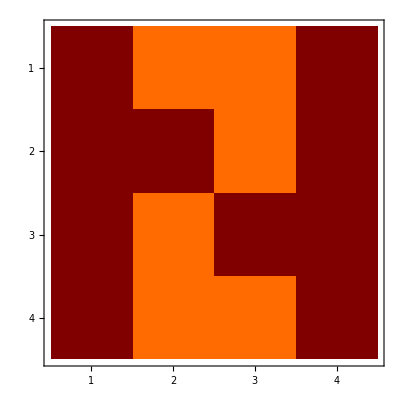

```mathematica
MatrixPlot[m]
```

```mathematica
ns = NullSpace[Transpose[m]]
```

{{1,1/l,1/l,1}}

```mathematica
Simplify[ns.m]
```

{{0,0,0,0}}